## Inicialize some functions

```mathematica
Remove["Global`*"]
```

```mathematica
<<CompiledFunctionTools`;
<<MaTeX`;
Needs["NumericalCalculus`"]
ParallelNeeds["NumericalCalculus`"]
compileOptions={CompilationTarget->"C",RuntimeOptions->{"EvaluateSymbolically"->False,"CatchMachineUnderflow"->False,"CatchMachineOverflow"->False}};
compileOptionsPar={Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed"};
font={BaseStyle->Directive[FontSize->12],AxesStyle->Directive[FontSize->12],TicksStyle->Directive[FontSize->12],LabelStyle->{FontFamily->"Latin Modern Roman",FontSize-> 12},BaseStyle->texStyle};
densityPlotOptions={PlotRange->Full,PlotLegends->Automatic,FrameLabel->MaTeX/@{"\\lambda","\\chi"},Evaluate@font,ColorFunction->"SunsetColors"};
```

ND::shdw: Symbol ND appears in multiple contexts {NumericalCalculus`,Notebook$$16$757801`}; definitions in context NumericalCalculus` may shadow or be shadowed by other definitions.

## First order perturbation Hamiltonian

```mathematica
$Assumptions={λ∈Reals,χ∈Reals};
```

```mathematica
δ[a_,b_]:=KroneckerDelta[a,b];
Je[sn_,j_,m_]:=√(j(j+1)-m(m+sn 1));
```

```mathematica
V1[jp_,mp_,j_,m_]:=1/4(Je[1,j,m+1]Je[1,j,m]δ[mp,m+2]+Je[-1,j,m-1]Je[-1,j,m]δ[mp,m-2]+δ[mp,m](Je[-1,j,m]Je[1,j,m-1]+Je[1,j,m]Je[-1,j,m+1] ))
V2[jp_,mp_,j_,m_]:=1/2(m+j)(Je[1,j,m]δ[mp,m+1]+Je[-1,j,m]δ[mp,m-1])+1/2(m+1+j)Je[1,j,m]δ[mp,m+1]+1/2(m-1+j)Je[-1,j,m]δ[mp,m-1]
V3[jp_,mp_,j_,m_]:=δ[mp,m](j+m)^2
Hd[jp_,mp_,j_,m_]:=m δ[jp,j]δ[mp,m]-δ[jp,j]/(2j)(λ V1[jp,mp,j,m]+χ V2[jp,mp,j,m]+χ^2 V3[jp,mp,j,m])
```

```mathematica
nn=5;
jj=nn/2; 
dim=nn+1;
f[mp_,m_]:=Hd[jj,mp,jj,m];
HH=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
H[λ_,χ_]=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];
```

```mathematica
If[ConjugateTranspose@H[2,7]==H[2,7],Print["Probably is Hermitean"],Print["THIS IS NOT Hermitean"]]
H[λ,χ]//MatrixForm//FullSimplify
```

Probably is Hermitean

(-5/2-λ/4 | -χ/(2 √5) | -λ/(√10) | 0 | 0 | 0
-χ/(2 √5) | 1/20 (-30-13 λ-4 χ^2) | -(3 √2 χ)/5 | -(3 λ)/(5 √2) | 0 | 0
-λ/(√10) | -(3 √2 χ)/5 | 1/20 (-17 λ-2 (5+8 χ^2)) | -(3 χ)/2 | -(3 λ)/(5 √2) | 0
0 | -(3 λ)/(5 √2) | -(3 χ)/2 | 1/20 (10-17 λ-36 χ^2) | -(7 √2 χ)/5 | -λ/(√10)
0 | 0 | -(3 λ)/(5 √2) | -(7 √2 χ)/5 | 1/20 (30-13 λ-64 χ^2) | -(9 χ)/(2 √5)
0 | 0 | 0 | -λ/(√10) | -(9 χ)/(2 √5) | 5/2-λ/4-5 χ^2)

```mathematica
DH1[λ_,χ_]=D[H[λ,χ],λ];
DH2[λ_,χ_]=D[H[λ,χ],χ];
g[λ_,χ_]:=Module[{g11,g12,g22,energies,eigenvectors},
energies=Eigenvalues[H[λ,χ]];
eigenvectors=Map[Normalize,Eigenvectors[H[λ,χ]]];
g11=Re@Sum[((Conjugate[eigenvectors[[1]]].DH1[λ,χ].eigenvectors[[i]])(Conjugate[eigenvectors[[i]]].DH1[λ,χ].eigenvectors[[1]]))/(energies[[1]]-energies[[i]])^2,{i,2,dim}];
g12=Re@Sum[(Conjugate[eigenvectors[[1]]].DH1[λ,χ].eigenvectors[[i]]Conjugate[eigenvectors[[i]]].DH2[λ,χ].eigenvectors[[1]])/(energies[[1]]-energies[[i]])^2,{i,2,dim}];
g22=Re@Sum[((Conjugate[eigenvectors[[1]]].DH2[λ,χ].eigenvectors[[i]])(Conjugate[eigenvectors[[i]]].DH2[λ,χ].eigenvectors[[1]]))/(energies[[1]]-energies[[i]])^2,{i,2,dim}];
{{g11,g12},{g12,g22}}
]
```

```mathematica
DH1C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],λ],Evaluate@compileOptions];
DH2C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],χ],Evaluate@compileOptions];
gC[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort,en,eigNonSort,eig,g11,g12,g22,M1,M1T,M2,M2T,endif},
{enNonSort,eigNonSort}=Eigensystem[HC[λ,χ],Method->{"Banded"}];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
M1=Conjugate[eig⟦1⟧].DH1C[λ,χ].eig⟦#⟧&/@Range[2,dim];
M1T=Conjugate[eig⟦#⟧].DH1C[λ,χ].eig⟦1⟧&/@Range[2,dim];

M2=Conjugate[eig⟦1⟧].DH2C[λ,χ].eig⟦#⟧&/@Range[2,dim];
M2T=Conjugate[eig⟦#⟧].DH2C[λ,χ].eig⟦1⟧&/@Range[2,dim];
endif=(en⟦1⟧-en⟦#⟧)^2&/@Range[2,dim];
g11=Re@Sum[(M1⟦i⟧M1T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g12=Re@Sum[(M1⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g22=Re@Sum[(M2⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
{{g11,g12},{g12,g22}}
]
```

```mathematica
gC[1,1]
```

{{0.0287265,-0.207271},{-0.207271,1.51664}}

## Energies

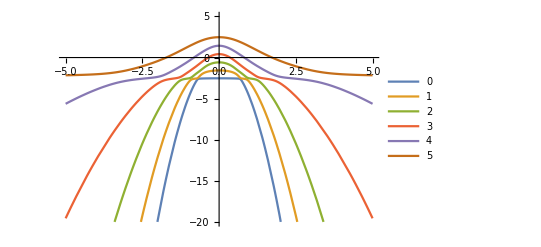

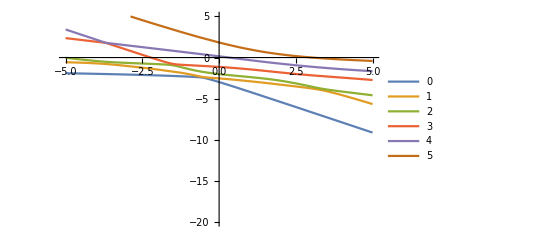

```mathematica
energies1=Eigenvalues[H[0.1,χ]];
energies2=Eigenvalues[H[λ,0.78]];
Plot[energies1,{χ,-5,5},PlotLegends->Range[0,10],PlotPoints->15,PlotRange->{Automatic,{-20,5}}]
Plot[energies2,{λ,-5,5},PlotLegends->Range[0,10],PlotPoints->5,PlotRange->{Automatic,{-20,5}}]
```

```mathematica
eigensys[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort,eigNonSort},
{enNonSort,eigNonSort}=Eigensystem[HC[λ,χ],Method->{"Banded"}];
Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First]
]
eigensys1[λ_?NumericQ,χ_?NumericQ]:=
Sort@Eigenvalues[HC[λ,χ],Method->{"Banded"}
]
```

```mathematica
Plot3D[Query[1]@ND[eigensys1[λ,x],{x,2},χ]+Query[1]@ND[eigensys1[l,χ],{l,2},λ],{λ,-3,10},{χ,-1,1},ColorFunction->"SunsetColors",PlotPoints=10,ExclusionsStyle->{None, Red},Exclusions->Automatic,ClippingStyle->None,PerformanceGoal->"Quality"]
```

## Metric tensor

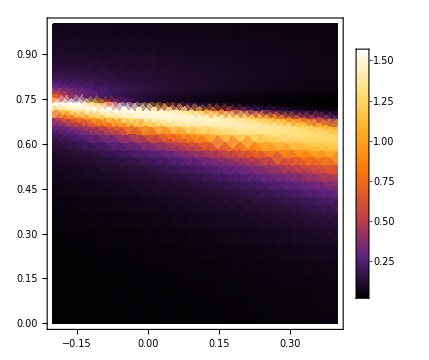
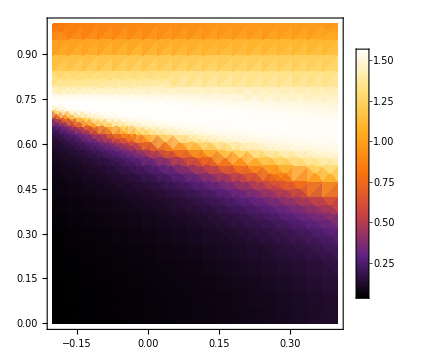
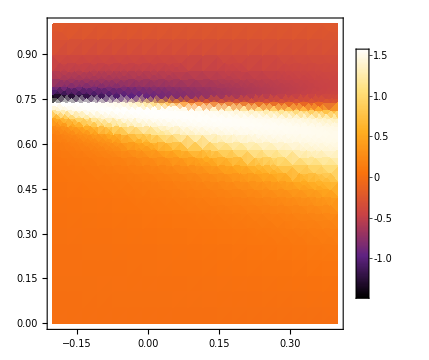

```mathematica
optDen={Evaluate@densityPlotOptions,PlotPoints->20,ImageSize->Medium};
{DensityPlot[ArcTan[gC[y,x]⟦1,1⟧],{y,-0.2,0.4},{x,0,1},Evaluate@optDen],
DensityPlot[ArcTan[gC[y,x]⟦2,2⟧],{y,-0.2,0.4},{x,0,1},Evaluate@optDen],
DensityPlot[ArcTan[gC[y,x]⟦1,2⟧],{y,-0.2,0.4},{x,0,1},Evaluate@optDen]}
```

#### Metric tensor determinant

```mathematica
DensityPlot[Det[gC[x,l]],{x,0,2.5},{l,0,2},Evaluate@densityPlotOptions,PlotPoints->300,ScalingFunctions->"Log10",PlotRange->Full]
```

-Graphics-

```mathematica
Plot3D[Det[gC[l,x]],{l,-0.5,2.5},{x,0,2},PlotPoints->50,Evaluate@font,ScalingFunctions->"Log10", ColorFunction->"SunsetColors",AxesLabel->MaTeX/@{"\\lambda","\\chi","Det(g)"}]
```

-Graphics3D-

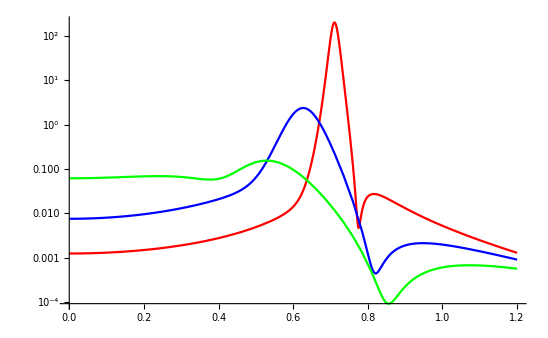

```mathematica
Plot[Evaluate[Det[gC[#,x]]&/@{0,0.5,1}],{x,0,1.2},PlotStyle->{Red,Blue,Green,Magenta,Purple},ScalingFunctions->"Log10"]
```

# Compiled geod function and Christoffel symbols

For huge matrices compute only first few energies and check for precission {vals,vecs}=Eigensystem[s,10]

Enable more functions to be compilable, for example Inverse

```mathematica
(*Internal`CompileValues[];(*to trigger auto-load*)ClearAttributes[Internal`CompileValues,ReadProtected];
syms=DownValues[Internal`CompileValues]/.HoldPattern[Verbatim[HoldPattern][Internal`CompileValues[sym_]]:>_]:>sym;
Complement[syms,Compile`CompilerFunctions[]]*)
```

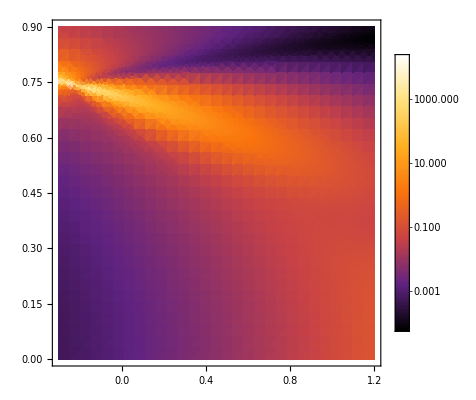

```mathematica
geodbg=DensityPlot[Det@gC[λ,χ],{λ,-0.3,1.2},{χ,0,0.9},Evaluate@densityPlotOptions,ScalingFunctions->"Log10",PlotPoints->30]
```

## Define area for derivative precision

```mathematica
(*{{3,-1/2,√(3/5)},{4,-0.333,0.756},{5,-0.2501,0.7454},{6,-0.2,0.738},{7,-0.173,0.7346},{8,-0.14,0.73},{9,-0.1255,0.7277},{10,-0.1111,0.7255},{11,-0.1,0.7238},{12,-0.09,0.7223},{13,-0.0834,0.7211},{14,-0.0769,0.72}};*)
{c1,c2}={-0.2501,0.7454};
derPiece[λ_?NumericQ,χ_?NumericQ]:=Piecewise[{{14,λ>1&&-0.4<χ<0.4}},Round[8+10/(0.8+(λ-c1)^2+(Abs[χ]-c2)^2)]];
derPieceC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@derPiece[λ,χ],Evaluate@compileOptions];
Plot3D[derPiece[λ,χ],{λ,-6,6},{χ,-3,3},PlotLegends->Automatic,PlotPoints->30,PlotRange->All,ColorFunction->"SunsetColors"]
```

-Graphics3D-

## Defining compiled functions

```mathematica
G1[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,c,l,dg,gInv},
derTerms=derPiece[λ,χ];
dg={ND[gC[l,χ],l,λ,Terms->derTerms],ND[gC[λ,c],c,χ,Terms->derTerms]};
gInv=1/2 Inverse[gC[λ,χ]];
{Sum[gInv[[1,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],Sum[gInv[[1,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],Sum[gInv[[1,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
G2[λ_?NumericQ,χ_?NumericQ]:=Module[{derTerms,c,l,dg,gInv},
derTerms=derPiece[λ,χ];
dg={ND[gC[l,χ],l,λ,Terms->derTerms],ND[gC[λ,c],c,χ,Terms->derTerms]};
gInv=1/2 Inverse[gC[λ,χ]];
{Sum[gInv[[2,ν]](dg[[1,1,ν]]+dg[[1,ν,1]]-dg[[ν,1,1]]),{ν,1,2}],Sum[gInv[[2,ν]](dg[[2,1,ν]]+dg[[1,ν,2]]-dg[[ν,1,2]]),{ν,1,2}],Sum[gInv[[2,ν]](dg[[2,2,ν]]+dg[[2,ν,2]]-dg[[ν,2,2]]),{ν,1,2}]}
]
```

```mathematica
(*G1[λ_?NumericQ,χ_?NumericQ]=Module[{derTerms,c,l,dg1,dg2,gInv1,gInv2},
derTerms=derPieceC[λ,χ];
{dg1,dg2}={ND[gC[l,χ],l,λ,Terms->derTerms],ND[gC[λ,c],c,χ,Terms->derTerms]};
{gInv1,gInv2}=(1/2)Inverse[gC[λ,χ]]⟦1,#⟧&/@{1,2};
{gInv1 dg1⟦1,1⟧+gInv2(2dg1⟦1,2⟧-dg2⟦1,1⟧),
gInv1 dg2⟦1,1⟧+gInv2 dg1⟦2,2⟧,
gInv1(2dg2⟦2,1⟧-dg1⟦2,2⟧)+gInv2 dg2⟦2,2⟧}
];
G2[λ_?NumericQ,χ_?NumericQ]=Module[{derTerms,c,l,dg1,dg2,gInv1,gInv2},
derTerms=derPieceC[λ,χ];
{dg1,dg2}={ND[gC[l,χ],l,λ,Terms->derTerms],ND[gC[λ,c],c,χ,Terms->derTerms]};
{gInv1,gInv2}=(1/2)Inverse[gC[λ,χ]]⟦2,#⟧&/@{1,2};
{ gInv1 dg1⟦1,1⟧+ gInv2(dg1⟦1,2⟧+dg1⟦2,1⟧-dg2⟦1,1⟧),
gInv1 dg2⟦1,1⟧+gInv2 dg1⟦2,2⟧,
gInv1(2dg2⟦2,1⟧-dg1⟦2,2⟧)+gInv2 dg2⟦2,2⟧}
]*)
(*Removing λ from derTerms executes normally, defining as := removes this problem, but then it cant select elements [[1,2]] WTFFFFFF??????
G1[λ_?NumericQ,χ_?NumericQ]=Module[{derTerms,c,l,dg1,dg2,gInv1,gInv2},
derTerms=5.5+λ;
{dg1,dg2}={ND[gC[l,χ],l,λ,Terms->Round@derTerms],ND[gC[λ,c],c,χ,Terms->Round@derTerms]};
{gInv1,gInv2}=(1/2)Inverse[gC[λ,χ]]⟦1,#⟧&/@{1,2};
dg1⟦1,1⟧
(*{gInv1 dg1⟦1,1⟧+gInv2(2dg1⟦1,2⟧-dg2⟦1,1⟧),
gInv1 dg2⟦1,1⟧+gInv2 dg1⟦2,2⟧,
gInv1(2dg2⟦2,1⟧-dg1⟦2,2⟧)+gInv2 dg2⟦2,2⟧}*)
];
ParallelTable[G1[1,i],{i,0,0.8,0.8}]*)
```

Check Christoffel symbols. If wrong, increase derTerms.

```mathematica
DensityPlot[ArcTan@G1[λ,χ]⟦#⟧,{λ,-0.2,1.2},{χ,0,1},Evaluate@densityPlotOptions,ImageSize->Medium,PlotPoints->5]&/@{1,2,3}
DensityPlot[ArcTan@G2[λ,χ]⟦#⟧,{λ,-0.2,1.2},{χ,0,1},Evaluate@densityPlotOptions,ImageSize->Medium,PlotPoints->5]&/@{1,2,3}
```

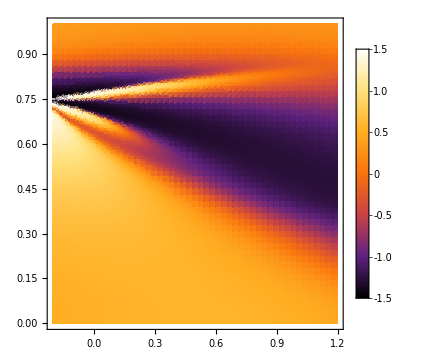
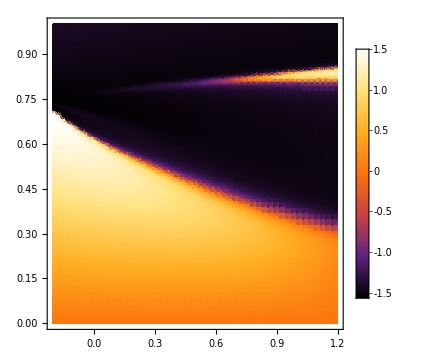
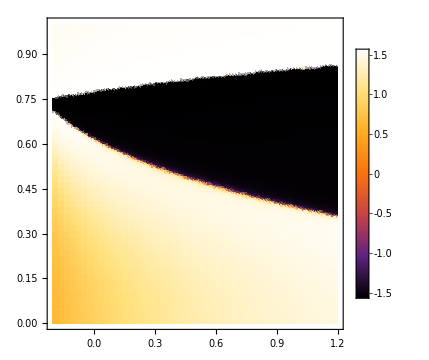

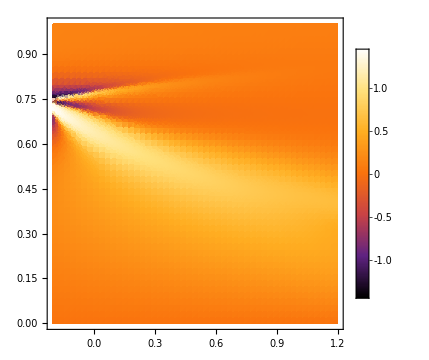
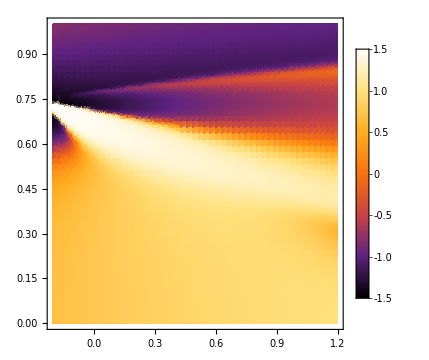
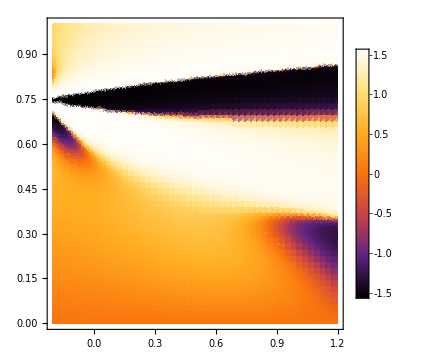

## Boundary value problem

```mathematica
tmax=10;
eq={
λ''[t]+G1[λ[t],χ[t]].{ λ'[t]^2,2 λ'[t]χ'[t], χ'[t]^2}==0,
χ''[t]+G2[λ[t],χ[t]].{ λ'[t]^2,2 λ'[t]χ'[t], χ'[t]^2}==0
};
dirichlet[i1_,i2_,f1_,f2_]:={λ[0]==i1,χ[0]==i2,λ[tmax]==f1,χ[tmax]==f2};
```

```mathematica
(*WorkingPrecision->20,Method->"StiffnessSwitching"*)
```

```mathematica
Timing@NDSolve[Join[eq,dirichlet[0,0,0,0.2]],{λ,χ},{t,0,tmax},PrecisionGoal->2,AccuracyGoal->2,WorkingPrecision->100,Method->"ExplicitRungeKutta"]
```

NDSolve::precw: The precision of the differential equation ({{G1[λ[t],χ[t]].{((«1»)^(«1»)[«1»])^2,2 («1»)^(«1»)[«1»] («1»)^(«1»)[«1»],((«1»)^(«1»)[«1»])^2}+λ''[t]==0,G2[λ[t],χ[t]].{((«1»)^(«1»)[«1»])^2,2 («1»)^(«1»)[«1»] («1»)^(«1»)[«1»],((«1»)^(«1»)[«1»])^2}+χ''[t]==0,λ[0]==0,χ[0]==0,λ[10]==0,χ[10]==0.2},{},{},{},{}}) is less than WorkingPrecision (100.).

{37.117,{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}}}

```mathematica
(*solP=ParametricNDSolve[Join[eq,dirichlet[0,0,0.3,f2]],{λ,χ},{t,0,tmax},{f2},PrecisionGoal->2,AccuracyGoal->2]
ParametricPlot[Evaluate@Table[{λ[f2][t],χ[f2][t]}/.solP,{f2,0,2,1}],{t,0,10},PlotRange->All]*)
```

```mathematica
Plot[Evaluate[x[t]/.sols],{t,0,10},PlotStyle->{Black,Blue,Green}]
```

```mathematica
solM=Quiet@ParallelTable[NDSolve[Join[eq,dirichlet[0,0,1,i]],{λ,χ},{t,0,tmax},PrecisionGoal->2,AccuracyGoal->2],{i,0,0.8,0.2}]
```

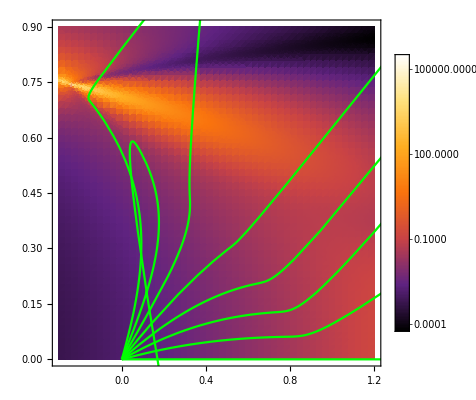

```mathematica
geodBoundary=ParametricPlot[{λ[t],χ[t]}/.solM2,{t,0,tmax},PlotRange->All,Frame->True,PlotStyle->Green];
Show[{geodbg,geodBoundary}]
```

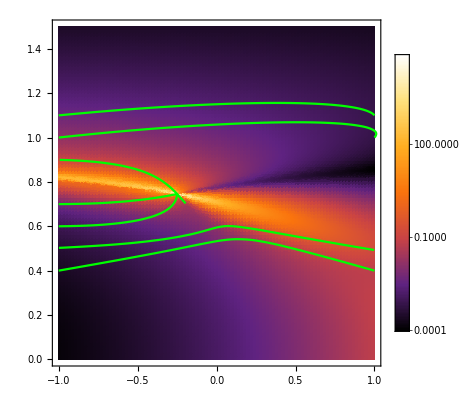
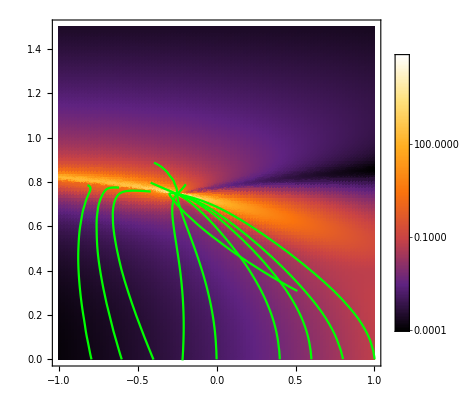
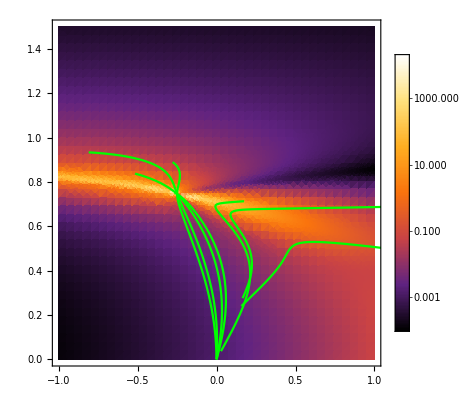
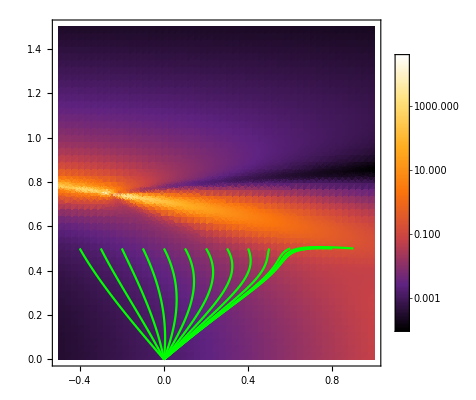
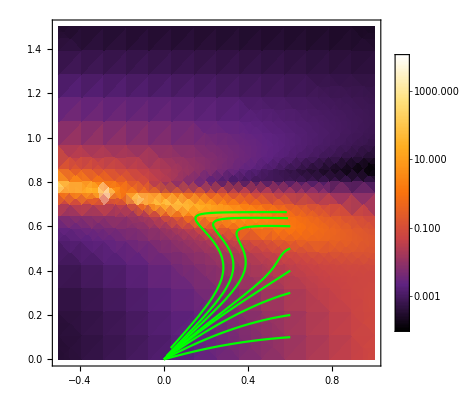
```mathematica
RungeKutta
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-
```

## Initial value problem

```mathematica
tmaxI=10;
cauchy[l1_,x1_,l2_,x2_]:={λ[0]==l1,χ[0]==x1,λ'[0]==l2,χ'[0]==x2};
```

```mathematica
sol=Quiet@NDSolve[Join[eq,cauchy[0,0,Cos[3],Sin[3]]],{λ,χ},{t,0,1000},PrecisionGoal->2,AccuracyGoal->2]
```

{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}}

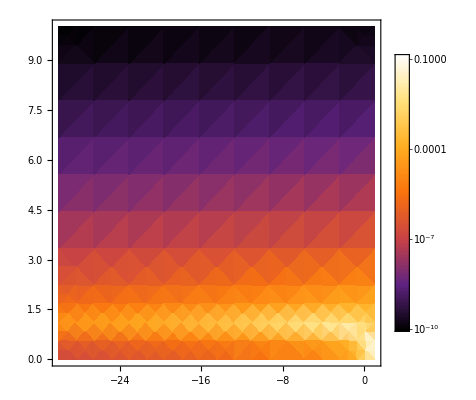

```mathematica
geodbg=DensityPlot[Det@gC[λ,χ],{λ,-30,1},{χ,0,10},Evaluate@densityPlotOptions,ScalingFunctions->"Log10",PlotPoints->10];
geodInitial=ParametricPlot[{λ[t],χ[t]}/.sol,{t,0,tmaxI},PlotRange->All,Frame->True,PlotStyle->Green];
Show[{geodbg,geodInitial}]
```

```mathematica
solMulti=Quiet@ParallelTable[NDSolve[Join[eq,cauchy[0,0,Cos[θ],Sin[θ]]],{λ,χ},{t,0,tmaxI},AccuracyGoal->2,PrecisionGoal->2],{θ,0,1,1/30}]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.000291409,-15.3933},{-15.3933,5.5882×10^6}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.000294612,-17.5377},{-17.5377,5.88768×10^6}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.00774567,123.897},{123.897,2.07323×10^6}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.00773447,124.713},{124.713,2.10303×10^6}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.00441516,49.9128},{49.9128,580032.}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0043997,49.9481},{49.9481,582882.}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0117014,114.627},{114.627,1.14779×10^6}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0117014,114.627},{114.627,1.14779×10^6}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0116905,114.725},{114.725,1.1508×10^6}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

NDSolve::ndsz: At Notebook$$91$216541`t == 7.74799, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At Notebook$$91$216541`t == 7.80022, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At Notebook$$91$216541`t == 7.74561, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At Notebook$$91$216541`t == 7.76174, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At Notebook$$91$216541`t == 7.78384, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At Notebook$$91$216541`t == 7.78, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0000118356,0.38816},{0.38816,20898.9}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0000328838,8.7459},{8.7459,2.51485×10^6}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.000624986,10.7555},{10.7555,198165.}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.000490358,8.87397},{8.87397,173440.}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

NDSolve::ndsz: At Notebook$$91$216541`t == 8.48247, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At Notebook$$91$216541`t == 7.83087, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At Notebook$$91$216541`t == 7.8981, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At Notebook$$91$216541`t == 7.83055, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{6.03219×10^-10,-3.27325×10^-7},{-3.27325×10^-7,0.000177624}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{5.93822×10^-10,-3.23286×10^-7},{-3.23286×10^-7,0.000176009}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

NDSolve::ndcf: Repeated convergence test failure at Notebook$$91$216541`t == 7.72248; unable to continue.

NDSolve::ndsz: At Notebook$$91$216541`t == 7.72051, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At Notebook$$91$216541`t == 7.63827, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At Notebook$$91$216541`t == 9.15412, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At Notebook$$91$216541`t == 7.96101, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At Notebook$$91$216541`t == 7.59792, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At Notebook$$91$216541`t == 8.0486, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At Notebook$$91$216541`t == 9.93558, step size is effectively zero; singularity or stiff system suspected.

{{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}},{{λ→InterpolatingFunction[…],χ→InterpolatingFunction[…]}}}

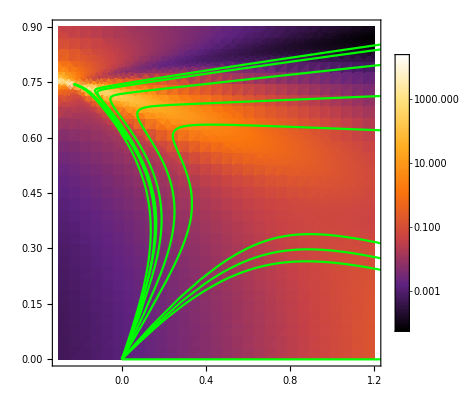

```mathematica
geodInitial=ParametricPlot[{λ[t],χ[t]}/.solMulti,{t,0,tmaxI},PlotRange->All,Frame->True,PlotStyle->Green];
Show[{geodbg,geodInitial}]
```

# Direct minimalization

Find geodesics by minimizing the expression for fidelity.

# Singularity and stuff

```mathematica
nn=5;
jj=nn/2; 
f[mp_,m_]:=Hd[jj,mp,jj,m];
HH=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
H[λ_,χ_]=Table[f[mp,m],{mp,-jj,jj},{m,-jj,jj}];
HC=Compile[{{λ,_Real},{χ,_Real}},Evaluate@HH,Evaluate@compileOptions];
```

```mathematica
DH1C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],λ],Evaluate@compileOptions];
DH2C=Compile[{{λ,_Real},{χ,_Real}},Evaluate@D[H[λ,χ],χ],Evaluate@compileOptions];
gC[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort,en,eigNonSort,eig,g11,g12,g22,M1,M1T,M2,M2T,endif},
{enNonSort,eigNonSort}=Eigensystem[HC[λ,χ],Method->{"Banded"}];
{en,eig}=Transpose@SortBy[Transpose[{enNonSort,eigNonSort}],First];
M1=Conjugate[eig⟦1⟧].DH1C[λ,χ].eig⟦#⟧&/@Range[2,dim];
M1T=Conjugate[eig⟦#⟧].DH1C[λ,χ].eig⟦1⟧&/@Range[2,dim];
M2=Conjugate[eig⟦1⟧].DH2C[λ,χ].eig⟦#⟧&/@Range[2,dim];
M2T=Conjugate[eig⟦#⟧].DH2C[λ,χ].eig⟦1⟧&/@Range[2,dim];
endif=(en⟦1⟧-en⟦#⟧)^2&/@Range[2,dim];
g11=Re@Sum[(M1⟦i⟧M1T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g12=Re@Sum[(M1⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
g22=Re@Sum[(M2⟦i⟧M2T⟦i⟧)/endif⟦i⟧,{i,1,dim-1}];
{{g11,g12},{g12,g22}}
]
```

```mathematica
maxPoints=Quiet@Table[FindMaximum[Det[gC[λ,χ]],{{λ,i},{χ,j}}],{i,-5,5,0.1},{j,0,2,0.1}];
```

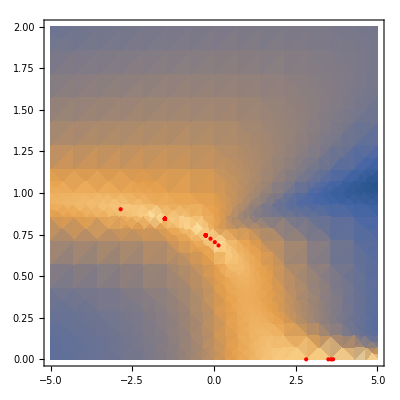

```mathematica
maxPointsD=DeleteDuplicates@maxPoints;
Show[DensityPlot[Det@gC[λ,χ],{λ,-5,5},{χ,0,2},ScalingFunctions->"Log10"],Graphics[{Red,PointSize[Large],Point[{λ,χ}/.Map[Last,maxPointsD,2]]}]]
```

```mathematica
Manipulate[DensityPlot[Det@gC[λ,χ],{λ,λmin,λmax},{χ,χmin,χmax},PlotPoints->PPoints,ScalingFunctions->"Log"],
{{λmin,-0.15},-2,0},{{λmax,0},-2,0},{{χmin,0.7},0,1},{{χmax,0.75},0,1},{{PPoints,30},5,100,1}]
```

```mathematica
gSing={{4,-0.333,0.756},{5,-0.2501,0.7454},{6,-0.2,0.738},{7,-0.173,0.7346},{8,-0.14,0.73},{9,-0.1255,0.7277},{10,-0.1111,0.7255},{11,-0.1,0.7238},{12,-0.09,0.7223},{13,-0.0834,0.7211},{14,-0.0769,0.72}};
```

```mathematica
ListPointPlot3D[gSing,Filling->Bottom]
```

-Graphics3D-

```mathematica
bA=ContourPlot[χ^2==(1-λ)/(2-λ),{λ,-1,1},{χ,0,1}];
```

```mathematica
pts=Transpose[Transpose[gSing]⟦#⟧&/@{1,2}];
ptsf=Transpose[{(-Transpose[gSing]⟦1⟧+13)/16,Transpose[gSing]⟦2⟧+1}];
Manipulate[Show[bA,ListPlot[
Transpose[{-s Transpose[gSing]⟦1⟧+a,s1 Transpose[gSing]⟦2⟧+b}
],PlotStyle->Red]],{{a,1.7},0,15},{{s,0.2},0,1},{{b,0.95},0,2},{{s1,2},0,3}]
```

Part::partw: Part 2 of Transpose[gSing] does not exist.

Transpose::nmtx: The first two levels of {1.7-0.2 gSing,0.95+2 Transpose[gSing]⟦2⟧} cannot be transposed.

Transpose::nmtx: The first two levels of {1.7-0.2 gSing,0.95+2. Transpose[gSing]⟦2⟧} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListPlot::lpn: Transpose[{1.7-0.2 gSing,0.95+2. Transpose[gSing]⟦2⟧}] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[bA,ListPlot[Transpose[{1.7-0.2 gSing,0.95+2 Transpose[«1»]⟦2⟧}],PlotStyle→RGBColor[1, 0, 0]]].

Part::partw: Part 2 of Transpose[gSing] does not exist.

Transpose::nmtx: The first two levels of {1.7-0.2 gSing,0.95+2 Transpose[gSing]⟦2⟧} cannot be transposed.

Transpose::nmtx: The first two levels of {1.7-0.2 gSing,0.95+2. Transpose[gSing]⟦2⟧} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListPlot::lpn: Transpose[{1.7-0.2 gSing,0.95+2. Transpose[gSing]⟦2⟧}] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[bA,ListPlot[Transpose[{1.7-0.2 gSing,0.95+2 Transpose[«1»]⟦2⟧}],PlotStyle→RGBColor[1, 0, 0]]].

Part::partw: Part 2 of Transpose[gSing] does not exist.

Transpose::nmtx: The first two levels of {1.7-0.2 gSing,0.95+2 Transpose[gSing]⟦2⟧} cannot be transposed.

Transpose::nmtx: The first two levels of {1.7-0.2 gSing,0.95+2. Transpose[gSing]⟦2⟧} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListPlot::lpn: Transpose[{1.7-0.2 gSing,0.95+2. Transpose[gSing]⟦2⟧}] is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[bA,ListPlot[Transpose[{1.7-0.2 gSing,0.95+2 Transpose[«1»]⟦2⟧}],PlotStyle→RGBColor[1, 0, 0]]].

```mathematica
data23=Transpose[Transpose[gSing]⟦2;;3⟧];
model23=fa  t+fb;
fit23=FindFit[data23,model23,{fa,fb},t]
```

{fa→-0.14085,fb→0.709759}

```mathematica
data12=Transpose[Transpose[gSing]⟦1;;2⟧];
model12=fa+fb √((1-t)/(2-t));
fit12=FindFit[data12,model12,{fa,fb},t]
```

{fa→1.38881,fb→-1.41439}

```mathematica
data13=Transpose[{Transpose[gSing]⟦1⟧,Transpose[gSing]⟦3⟧}];
model13=fa+fb √((1-t)/(2-t));
fit13=FindFit[data13,model13,{fa,fb},t]
```

{fa→0.514709,fb→0.1987}

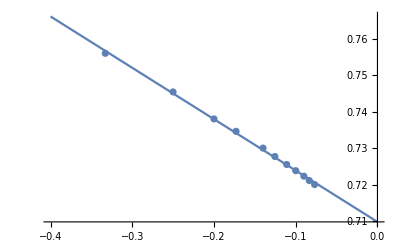

```mathematica
Show[Plot[model23/.fit23,{t,-0.4,0}],ListPlot@data23]
```

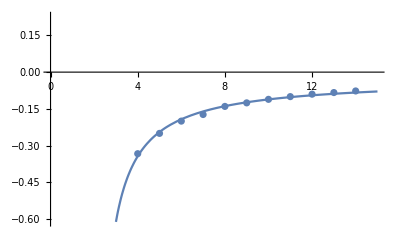

```mathematica
Show[Plot[model12/.fit12,{t,0,15}],ListPlot@data12]
```

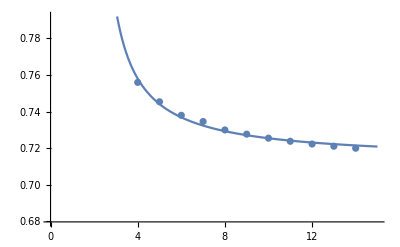

```mathematica
Show[Plot[model13/.fit13,{t,0,15}],ListPlot@data13]
```

### Energy difference singularity

```mathematica
enSing[λ_?NumericQ,χ_?NumericQ]:=Module[{enNonSort},
enNonSort=Eigenvalues[HC[λ,χ],Method->{"Banded"}];
Sort@enNonSort
]
Manipulate[DensityPlot[enSing[λ,χ]⟦1⟧-enSing[λ,χ]⟦2⟧,{λ,λmin,λmax},{χ,χmin,χmax},PlotPoints->20],
{{λmin,-0.5},-2,0},{{λmax,0},-2,0},{χmin,0,1},{{χmax,1},0,1},{{PPoints,15},5,100,1}]
```

Coordinates of singularities for different nn. For nn = 3 exist only one point {3, -0.5, 0.7746}, then at least 2.

```mathematica
sing2={{4,-0.3,0.8944},{5,-1.5,0.845},{6,-1,0.865},{7,-0.7527,0.7979}};
ListPointPlot3D[sing2,Filling->Bottom]
```

-Graphics3D-